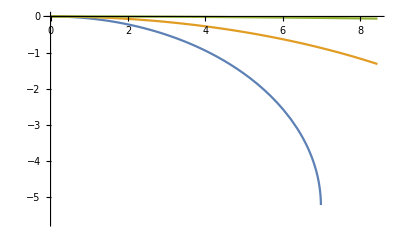

```mathematica
mm=1;
μm=10^-3;
n1=1.52; (*refractive index of the objective. guessed. common glass is 1.52*)
n2; (*refractive index of the immersion medium*)
W=8 mm; (*working distance of the objective in mm*)

Δf[y_,n2_]:=y √((n2/n1)^2(1+W^2/y^2)-1)-n2/n1 W  (*shift of the focal point in mm*)
(*plot of Δf*)
Plot[ {Δf[y,1.0],Δf[y,1.33],Δf[y,1.51]},{y,0,8.45},PlotRange->{{0,8.45},{-5.7,0}} ]
```